Efficient high-energy photon production in the supercritical QED regime

Matteo Tamburini and Sebastian Meuren, Phys Rev D 104, L091903 (2021)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Figure 2

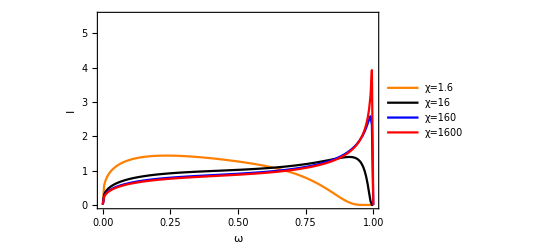

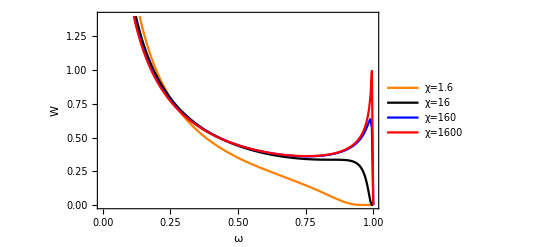

```mathematica
Clear[τc,ℏ,m,c,α,χ,γ,ω,d2Wdtdω,d2Idtdω,dWdt,dIdt]
Clear[dIdt00016,dIdt00160,dIdt01600,dIdt16000]
τc=ℏ/(m c^2);
ℏ=m=c=1;
α=1/137;
γ=1;
d2Wdtdω[ω_?NumericQ,χ_?NumericQ]:=d2Wdtdω[ω,χ]=α/(√3 π τc γ)((2+ω^2/(1-ω))BesselK[2/3,(2ω)/(3χ(1-ω))]-NIntegrate[BesselK[1/3,y],{y,(2ω)/(3χ(1-ω)),∞}])
d2Idtdω[ω_?NumericQ,χ_?NumericQ]:=d2Idtdω[ω,χ]=ω d2Wdtdω[ω,χ]
dWdt[χ_]:=NIntegrate[d2Wdtdω[ω,χ],{ω,0,1}]
dIdt[χ_]:=NIntegrate[d2Idtdω[ω,χ],{ω,0,1}]
(* normalization *)
dWdt00016=dWdt[1.6];dWdt00160=dWdt[16];dWdt01600=dWdt[160];dWdt16000=dWdt[1600];
(* *)
dIdt00016=dIdt[1.6];dIdt00160=dIdt[16];dIdt01600=dIdt[160];dIdt16000=dIdt[1600];
(* *)
Plot[{1/dIdt00016 d2Idtdω[ω,1.6],1/dIdt00160 d2Idtdω[ω,16],1/dIdt01600 d2Idtdω[ω,160],1/dIdt16000 d2Idtdω[ω,1600]},{ω,0,1},PlotPoints->4,Frame->True,FrameLabel->{"ω","I"},PlotRange->{0,5.5},PlotLegends->{"χ=1.6","χ=16","χ=160","χ=1600"},PlotStyle->{Orange,Black,Blue,Red}]

Plot[{1/dWdt00016 d2Wdtdω[ω,1.6],1/dWdt00160 d2Wdtdω[ω,16],1/dWdt01600 d2Wdtdω[ω,160],1/dWdt16000 d2Wdtdω[ω,1600]},{ω,0,1},PlotPoints->4,Frame->True,FrameLabel->{"ω","W"},PlotRange->{0,1.4},PlotLegends->{"χ=1.6","χ=16","χ=160","χ=1600"},PlotStyle->{Orange,Black,Blue,Red}]
```

## Prove eq 4

```mathematica
Clear[ωmin,ωmax,χ,ω,getωmin,getωmax,ωminTh,ωminExact,ωmaxTh,ωmaxExact]
ωmin=0.754+(15.7+0.146χ)/χ^2;
ωmax=1-(174+20χ)/(15 χ^2);
getωmin[χ_]:=(FindMinimum[{d2Wdtdω[ω,χ],0.1<ω<1},{ω,0.5}]//Quiet)[[2,1,2]]
getωmax[χ_]:=(FindMaximum[{d2Wdtdω[ω,χ],0.1<ω<1},{ω,0.8}]//Quiet)[[2,1,2]]
ωminTh=ParallelTable[{10^logχ,ωmin/.{χ->10^logχ}},{logχ,1.35,3.5,0.2}];
ωminExact=ParallelTable[{10^logχ,getωmin[10^logχ]},{logχ,1.35,3.5,0.2}];
ωmaxTh=ParallelTable[{10^logχ,ωmax/.{χ->10^logχ}},{logχ,1.35,3.5,0.2}];
ωmaxExact=ParallelTable[{10^logχ,getωmax[10^logχ]},{logχ,1.35,3.5,0.2}];
```

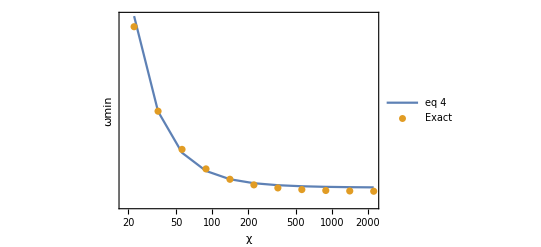

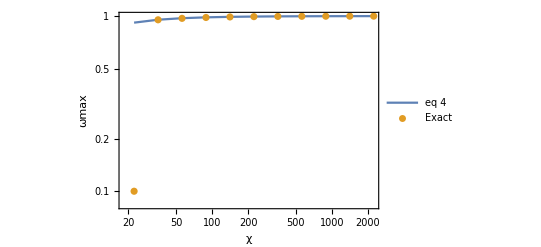

```mathematica
ListLogLogPlot[{ωminTh,ωminExact},PlotLegends->{"eq 4","Exact"},Frame->True,FrameLabel->{"χ","ωmin"},Joined->{True,False}]
ListLogLogPlot[{ωmaxTh,ωmaxExact},PlotLegends->{"eq 4","Exact"},Frame->True,FrameLabel->{"χ","ωmax"},Joined->{True,False}]
```

## Prove eq 5

```mathematica
Clear[ωmin,ωmax,χ,ω,getWmin,getWmax,ωminTh,ωminExact,ωmaxTh,ωmaxExact]
getWmin[χ_]:=(FindMinimum[{d2Wdtdω[ω,χ],0.1<ω<1},{ω,0.5}]//Quiet)[[1]]
getWmax[χ_]:=(FindMaximum[{d2Wdtdω[ω,χ],0.1<ω<1},{ω,0.8}]//Quiet)[[1]]
HTh=ParallelTable[{10^logχ,((1.315+0.315χ)/χ^(2/3))/.{χ->10^logχ}},{logχ,1.35,3.5,0.2}];
HExact=ParallelTable[{10^logχ,getWmax[10^logχ]/getWmin[10^logχ]},{logχ,1.35,3.5,0.2}];
```

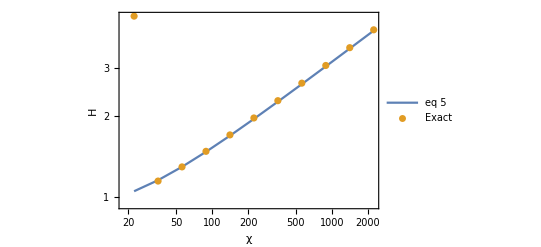

```mathematica
ListLogLogPlot[{HTh,HExact},PlotLegends->{"eq 5","Exact"},Frame->True,FrameLabel->{"χ","H"},Joined->{True,False}]
```

## Figure 4

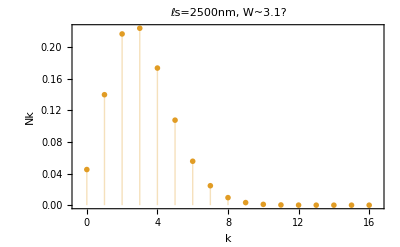

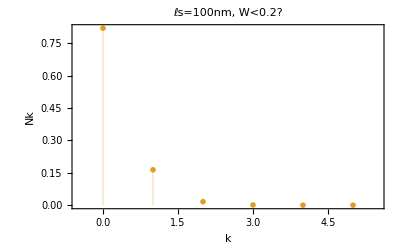

```mathematica
Clear[W,k,tab1,tab2]
tab1=ParallelTable[{k,-1 W^k/(k!)Exp[-W]},{k,0,16}];
tab2=ParallelTable[{k,W^k/(k!)Exp[-W]},{k,0,16}];
ListPlot[{tab1,tab2/.{W->3.1}},Filling->Bottom,PlotMarkers->"OpenMarkers",PlotRange->{{-0.5,16.5},All},Frame->True,FrameLabel->{"k","Nk"},PlotLabel->"ℓs=2500nm, W~3.1?"]
ListPlot[{tab1,tab2/.{W->0.2}},Filling->Bottom,PlotMarkers->"OpenMarkers",PlotRange->{{-0.5,5.5},All},Frame->True,FrameLabel->{"k","Nk"},PlotLabel->"ℓs=100nm, W<0.2?"]
```